Evaluate Cshaper.nb before evaluating this notebook.

```mathematica
NotebookDirectory[]
```

/home/jpd/Development/NICER/NICER-simulation/math/

```mathematica
Needs["CUDALink`"]
```

```mathematica
runShaperArgs = {
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
"Double",
"Integer32",
"Integer32",
"Integer32",
{"Double",_,"Output"}};
runShaperSource = Import[NotebookDirectory[]<>"PoissonShapers.cu", "Text"]
```

/*
Mathematica's CUDALink wraps user source in extern "C" {}
This causes trouble with headers that have C++ constructs in them.
Use the fact that CUDALink defines USING_CUDA_FUNCTION to repair this.
*/

#if USING_CUDA_FUNCTION
}
#endif

// Put any includes of C++isms here.

#include <curand_kernel.h>

#if USING_CUDA_FUNCTION
extern "C" {
#endif

#define SETTLE 200

__global__ void run_shapers ( 
	double *ucout, double *ucback, 	// unipolar shaper parameters
	double *bcout, double *bcback, 	// bipolar shaper parameters
	double noise,			// electrons/step
	int when,			// step at which pulse happens
	int pulse,			// pulse height, electrons
	int steps, 			// steps of simulation
	double *out 			// output array
	) {
	
	int thread = blockDim.x * blockIdx.x + threadIdx.x;
	curandState_t curand_state;
	double ucout0 = ucout[0];
	double ucout1 = ucout[1];
	double ucout2 = ucout[2];
	double ucout3 = ucout[3];
	double ucout4 = ucout[4];
	double ucout5 = ucout[5];
	double ucout6 = ucout[6];
	double ucback1 = ucback[0];
	double ucback2 = ucback[1];
	double ucback3 = ucback[2];
	double ucback4 = ucback[3];
	double ucback5 = ucback[4];
	double ucback6 = ucback[5];
	double ux1 = 0.0;
	double ux2 = 0.0;
	double ux3 = 0.0;
	double ux4 = 0.0;
	double ux5 = 0.0;
	double ux6 = 0.0;
	double uy, ufb;
	double bcout0 = bcout[0];
	double bcout1 = bcout[1];
	double bcout2 = bcout[2];
	double bcout3 = bcout[3];
	double bcout4 = bcout[4];
	double bcout5 = bcout[5];
	double bcout6 = bcout[6];
	double bcback1 = bcback[0];
	double bcback2 = bcback[1];
	double bcback3 = bcback[2];
	double bcback4 = bcback[3];
	double bcback5 = bcback[4];
	double bcback6 = bcback[5];
	double bx1 = 0.0;
	double bx2 = 0.0;
	double bx3 = 0.0;
	double bx4 = 0.0;
	double bx5 = 0.0;
	double bx6 = 0.0;
	double by, bfb;
	int i;

	curand_init ( 100951,
		thread,
		0,
		& curand_state );

	out += thread * steps * 2;	// two outputs per step per thread

	for ( i = -SETTLE; i < steps; i += 1) {
		
		double u = 0;		// input
		if ( i == when ) u = pulse;
		u += curand_poisson ( & curand_state, noise );

		uy = ucout0*u + ucout1*ux1 + ucout2*ux2 + ucout3*ux3 +
			ucout4*ux4 + ucout5*ux5 + ucout6*ux6;

		ufb = u + ucback1*ux1 + ucback2*ux2 + ucback3*ux3 + 
			ucback4*ux4 + ucback5*ux5 + ucback6*ux6;

		ux1 = ux2;
		ux2 = ux3;
		ux3 = ux4;
		ux4 = ux5;
		ux5 = ux6;
		ux6 = ufb;
		
		if ( i >= 0 ) *out++ = uy;

		by = bcout0*u + bcout1*bx1 + bcout2*bx2 + bcout3*bx3 +
			bcout4*bx4 + bcout5*bx5 + bcout6*bx6;

		bfb = u + bcback1*bx1 + bcback2*bx2 + bcback3*bx3 + 
			bcback4*bx4 + bcback5*bx5 + bcback6*bx6;

		bx1 = bx2;
		bx2 = bx3;
		bx3 = bx4;
		bx4 = bx5;
		bx5 = bx6;
		bx6 = bfb;
		
		if ( i >= 0 ) *out++ = by;
	
	}
}

```mathematica
runShaper=CUDAFunctionLoad[runShaperSource,"run_shapers",runShaperArgs,256,"XCompilerInstallation"->"/usr/bin/gcc-8"]
```

CUDAFunction[<>,run_shapers,{{Double,_,Input},{Double,_,Input},{Double,_,Input},{Double,_,Input},Double,Integer32,Integer32,Integer32,{Double,_,Output}}]

```mathematica
nonoise=runShaper[
cout[uModel/.commonValues/.slowValues/.τsub],
cback[uModel/.commonValues/.slowValues/.τsub],
cout[bModel/.commonValues/.slowValues/.τsub],
cback[bModel/.commonValues/.slowValues/.τsub],
0.0,
0,
1,
250,
ConstantArray[0,{1024,250,2}],1024] ;
```

```mathematica
Dimensions[nonoise]
```

{1,1024,250,2}

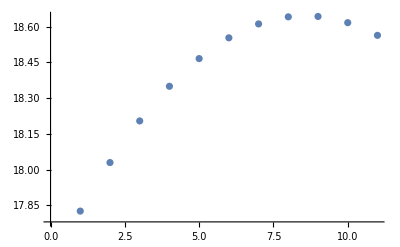

```mathematica
ListPlot[nonoise[[1,1,55;;65,1]]]
```

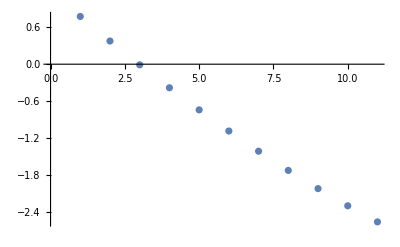

```mathematica
ListPlot[nonoise[[1,1,55;;65,2]]]
```

Peak bipolar response to unit input, for scaling trigger level.

```mathematica
bnorm = Max@@nonoise[[1,1,All,2]]
```

8.89099

```mathematica
eventsArgs = {
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
{"Double",_,"Input"},
"Double",
"Integer32",
"Integer32",
"Integer32",
"Double",
{"Double",_,"Output"},
{"Integer32",_,"Output"},
{"Double",_,"Output"}};
eventsSource = Import[NotebookDirectory[]<>"PoissonEvents.cu", "Text"]
```

/*
Mathematica's CUDALink wraps user source in extern "C" {}
This causes trouble with headers that have C++ constructs in them.
Use the fact that CUDALink defines USING_CUDA_FUNCTION to repair this.
*/

#if USING_CUDA_FUNCTION
}
#endif

// Put any includes of C++isms here.

#include <curand_kernel.h>

#if USING_CUDA_FUNCTION
extern "C" {
#endif

#define SETTLE 200

__global__ void events ( 
	double *ucout, double *ucback, 	// unipolar shaper parameters
	double *bcout, double *bcback, 	// bipolar shaper parameters
	double noise,			// electrons/step
	int when,			// step at which pulse happens
	int pulse,			// pulse height, electrons
	int steps, 			// steps of simulation
	double thresh,			// trigger threshold
	double *ft,			// forced trigger sample
	int *tz,			// time of zero crossing
	double *ph			// pulse height
	) {
	
	int thread = blockDim.x * blockIdx.x + threadIdx.x;
	curandState_t curand_state;
	double ucout0 = ucout[0];
	double ucout1 = ucout[1];
	double ucout2 = ucout[2];
	double ucout3 = ucout[3];
	double ucout4 = ucout[4];
	double ucout5 = ucout[5];
	double ucout6 = ucout[6];
	double ucback1 = ucback[0];
	double ucback2 = ucback[1];
	double ucback3 = ucback[2];
	double ucback4 = ucback[3];
	double ucback5 = ucback[4];
	double ucback6 = ucback[5];
	double ux1 = 0.0;
	double ux2 = 0.0;
	double ux3 = 0.0;
	double ux4 = 0.0;
	double ux5 = 0.0;
	double ux6 = 0.0;
	double uy, ufb;
	double bcout0 = bcout[0];
	double bcout1 = bcout[1];
	double bcout2 = bcout[2];
	double bcout3 = bcout[3];
	double bcout4 = bcout[4];
	double bcout5 = bcout[5];
	double bcout6 = bcout[6];
	double bcback1 = bcback[0];
	double bcback2 = bcback[1];
	double bcback3 = bcback[2];
	double bcback4 = bcback[3];
	double bcback5 = bcback[4];
	double bcback6 = bcback[5];
	double bx1 = 0.0;
	double bx2 = 0.0;
	double bx3 = 0.0;
	double bx4 = 0.0;
	double bx5 = 0.0;
	double bx6 = 0.0;
	double by, bfb;
	
	int trigger = 0;
	
	int i;

	curand_init ( 100951,
		thread,
		0,
		& curand_state );

	for ( i = -SETTLE; i < steps; i += 1) {
		
		double u = 0;		// input
		if ( i == when ) u = pulse;
		u += curand_poisson ( & curand_state, noise );

		uy = ucout0*u + ucout1*ux1 + ucout2*ux2 + ucout3*ux3 +
			ucout4*ux4 + ucout5*ux5 + ucout6*ux6;

		ufb = u + ucback1*ux1 + ucback2*ux2 + ucback3*ux3 + 
			ucback4*ux4 + ucback5*ux5 + ucback6*ux6;

		ux1 = ux2;
		ux2 = ux3;
		ux3 = ux4;
		ux4 = ux5;
		ux5 = ux6;
		ux6 = ufb;

		by = bcout0*u + bcout1*bx1 + bcout2*bx2 + bcout3*bx3 +
			bcout4*bx4 + bcout5*bx5 + bcout6*bx6;

		bfb = u + bcback1*bx1 + bcback2*bx2 + bcback3*bx3 + 
			bcback4*bx4 + bcback5*bx5 + bcback6*bx6;

		bx1 = bx2;
		bx2 = bx3;
		bx3 = bx4;
		bx4 = bx5;
		bx5 = bx6;
		bx6 = bfb;
		
		if( i == when - 1 ) ft[ thread ] = uy;
		
		if ( i >= 0 ) {
			if( trigger && by < 0.0 ) {
				tz[ thread ] = i;
				ph[ thread] = uy;
				trigger = 0;
			} else if( by > thresh ) trigger = 1;
		}
	}
}

```mathematica
events=CUDAFunctionLoad[eventsSource,"events",eventsArgs,256,"XCompilerInstallation"->"/usr/bin/gcc-8"]
```

CUDAFunction[<>,events,{{Double,_,Input},{Double,_,Input},{Double,_,Input},{Double,_,Input},Double,Integer32,Integer32,Integer32,Double,{Double,_,Output},{Integer32,_,Output},{Double,_,Output}}]

```mathematica
noNoiseEvents=events[
cout[uModel/.commonValues/.slowValues/.τsub],
cback[uModel/.commonValues/.slowValues/.τsub],
cout[bModel/.commonValues/.slowValues/.τsub],
cback[bModel/.commonValues/.slowValues/.τsub],
0.0,
0,
1,
250,
bnorm/2,
ConstantArray[0,1024],
ConstantArray[0,1024],
ConstantArray[0,1024]
] ;
```

```mathematica
Dimensions[noNoiseEvents]
```

{3,1024}

```mathematica
unorm=noNoiseEvents[[3,1]]
```

18.2039

1 keV in electrons

```mathematica
keV=1000/3.6
```

277.778

```mathematica
tstep = N[τ/.τsub]
```

9.68814×10^-9

```mathematica
noiseRun[ph_,load_, thresh_,n_]:=events[
cout[uModel/.commonValues/.slowValues/.τsub],
cback[uModel/.commonValues/.slowValues/.τsub],
cout[bModel/.commonValues/.slowValues/.τsub],
cback[bModel/.commonValues/.slowValues/.τsub],
load tstep,
0,
Round[ph keV],
100,
thresh keV bnorm,
ConstantArray[0,n],
ConstantArray[0,n],
ConstantArray[0,n]
] {1/unorm/keV,tstep,1/unorm/keV}
```

```mathematica
noiseStats[ph_,load_, thresh_,n_]:=With[
{r=noiseRun[ph,load,thresh,n]},
{Mean[r[[1]]],Variance[r[[1]]],Mean[r[[3]]]-ph,Variance[r[[3]]]}]
```

```mathematica
ns=Transpose[Table[Transpose[{{n,n,n,n},noiseStats[1,n,0.25,16384]}],{n,0,2 10^7,10^6}]]
```

{{{0,0.},{1000000,0.00216033},{2000000,0.00431934},{3000000,0.00650079},{4000000,0.00864858},{5000000,0.0108163},{6000000,0.0130044},{7000000,0.0151475},{8000000,0.0173215},{9000000,0.0195079},{10000000,0.0216668},{11000000,0.0238377},{12000000,0.0260092},{13000000,0.0282153},{14000000,0.0304079},{15000000,0.0325821},{16000000,0.0347541},{17000000,0.0369172},{18000000,0.0390536},{19000000,0.0412174},{20000000,0.0433947}},{{0,0.},{1000000,5.77683×10^-6},{2000000,0.000011686},{3000000,0.0000176525},{4000000,0.0000238738},{5000000,0.0000298134},{6000000,0.0000362483},{7000000,0.0000417173},{8000000,0.0000474163},{9000000,0.000053607},{10000000,0.0000597607},{11000000,0.0000656624},{12000000,0.0000715639},{13000000,0.0000777429},{14000000,0.0000840178},{15000000,0.0000898388},{16000000,0.0000954357},{17000000,0.000101269},{18000000,0.000106952},{19000000,0.000112717},{20000000,0.000118445}},{{0,0.0008},{1000000,0.00479378},{2000000,0.00766007},{3000000,0.0101019},{4000000,0.0124722},{5000000,0.0147319},{6000000,0.016982},{7000000,0.0192634},{8000000,0.0214594},{9000000,0.0236631},{10000000,0.0258678},{11000000,0.0281705},{12000000,0.030322},{13000000,0.0325074},{14000000,0.0347011},{15000000,0.0369141},{16000000,0.0391084},{17000000,0.0413293},{18000000,0.0435163},{19000000,0.0456423},{20000000,0.0477906}},{{0,0.},{1000000,0.0000201602},{2000000,0.0000271603},{3000000,0.0000329886},{4000000,0.0000385348},{5000000,0.0000441053},{6000000,0.0000498546},{7000000,0.0000557298},{8000000,0.0000615131},{9000000,0.0000668982},{10000000,0.0000735759},{11000000,0.0000787908},{12000000,0.0000841246},{13000000,0.0000895058},{14000000,0.0000958021},{15000000,0.000101189},{16000000,0.000107493},{17000000,0.000113335},{18000000,0.000119146},{19000000,0.000124258},{20000000,0.000129257}}}

```mathematica
ListLogLogPlot[{Callout[ns[[1]],"Mean[forced trigger]"],Callout[{#[[1]],#[[2]]100}&/@ns[[2]],"Variance[forced trigger]×100"],Callout[ns[[3]],"Mean[1 keV bias]"],Callout[{#[[1]],#[[2]]100}&/@ns[[4]],"Variance[1 keV]×100"]},ImageSize->Full,AxesLabel->{"Electrons/second","keV"}]
```

```mathematica
0.5 keV bnorm
```

1234.86

```mathematica
1 keV
```

277.778

```mathematica
shaperRun[ph_,load_,n_]:=runShaper[
cout[uModel/.commonValues/.slowValues/.τsub],
cback[uModel/.commonValues/.slowValues/.τsub],
cout[bModel/.commonValues/.slowValues/.τsub],
cback[bModel/.commonValues/.slowValues/.τsub],
load tstep,
0,
Round[ph keV],
250,
ConstantArray[0,{n,250,2}],n]
```

```mathematica
ListPlot[shaperRun[1, 2 10^7,32][[1,4,All,2]]]
```